```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\WGong.xlsx"]
```

```mathematica
data1={{10.,0.029900000000000003},{11.,0.033109999999999994},{12.,0.036359999999999996},{12.9,0.039345},{14.5,0.044660000000000005},{16.,0.049600000000000005},{17.5,0.05460000000000001},{19.,0.05966},{20.9,0.06604399999999999},{22.9,0.072822},{25.,0.08025},{27.,0.08748},{29.,0.09454},{31.,0.10167999999999999},{33.,0.1089},{34.,0.11288000000000001},{35.,0.11655000000000001},{37.,0.12394999999999999},{39.,0.13182},{40.,0.1356}};
```

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\BGong.xlsx"]
```

```mathematica
data2={{10.,0.029700000000000004},{11.,0.03278},{12.,0.036000000000000004},{13.,0.03913},{14.,0.04228},{15.,0.04545},{16.5,0.050325},{18.,0.055080000000000004},{20.,0.0616},{22.,0.0682},{24.,0.07488},{25.4,0.079756},{27.,0.08451},{28.4,0.08946},{30.,0.09509999999999999},{31.5,0.10017000000000001},{32.9,0.104622},{34.,0.10846}};
```

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\GGong.xlsx"]
```

```mathematica
data3={{10.,0.0313},{11.4,0.03591},{12.9,0.040893},{15.,0.048},{16.5,0.052965000000000005},{17.9,0.057638},{19.5,0.06318},{21.,0.06825},{22.5,0.07335},{24.,0.07823999999999999},{25.4,0.083312},{27.,0.08883},{28.4,0.09371999999999998},{30.,0.09899999999999999},{32.,0.10624},{34.,0.11356000000000001},{35.9,0.120624},{37.9,0.127723},{40.,0.136}}
```

{{10.,0.0313},{11.4,0.03591},{12.9,0.040893},{15.,0.048},{16.5,0.052965},{17.9,0.057638},{19.5,0.06318},{21.,0.06825},{22.5,0.07335},{24.,0.07824},{25.4,0.083312},{27.,0.08883},{28.4,0.09372},{30.,0.099},{32.,0.10624},{34.,0.11356},{35.9,0.120624},{37.9,0.127723},{40.,0.136}}

```mathematica
a1=ListPlot[data1];
```

```mathematica
b1=ListPlot[data2];
```

```mathematica
c1=ListPlot[data3];
```

```mathematica
a=LinearModelFit[data1,x,x]
```

FittedModel[-0.00646626+0.00351156 x]

```mathematica
b=LinearModelFit[data2,x,x]
```

FittedModel[-0.00368639+0.00328531 x]

```mathematica
c=LinearModelFit[data3,x,x]
```

FittedModel[-0.00425297+0.00346746 x]

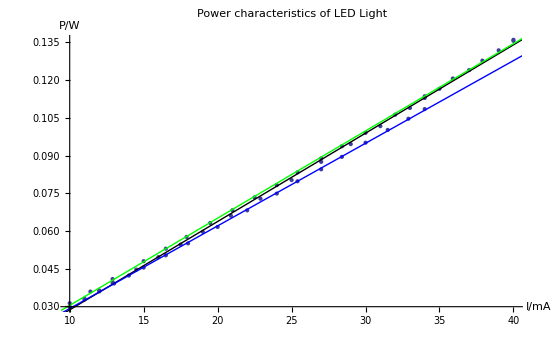

```mathematica
Show[a1,b1,c1,Plot[a[x],{x,0,50},PlotStyle->Black],Plot[b[x],{x,0,50},PlotStyle->Blue],Plot[c[x],{x,0,50},PlotStyle->Green],AxesLabel->{"I/mA","P/W"},PlotLabel->"Power characteristics of LED Light"]
```